# FindRandomGridMazeSolution

Find a solution to a random maze

## Definition

```mathematica
PositiveIntegerQ//ClearAll
PositiveIntegerQ[n_]:=And@@{IntegerQ[n],TrueQ[n∈PositiveIntegers]}
```

```mathematica
ClearAll[FindRandomGridMazeSolution]
```

```mathematica
FindRandomGridMazeSolution::usage="FindRandomGridMazeSolution[{m,n}] finds a solution and other data for a random grid maze of size m by n. FindRandomGridMazeSolution[{m,n},property] computes property which can be a single string or a list of properties.";
FindRandomGridMazeSolution[{m1_?PositiveIntegerQ /;!(m1<=1)(*equivalent to n>1. The reason I impose this constraint is the graph needs to be big enough to take away edges and still have edges. GridGraph[{1,1}] has no edges.*),n1_?PositiveIntegerQ/;!(n1<=1)(*equivalent to n>1*)}]:=Module[{g,maze,m,solvedmaze,shortestPath,start,end,shortestPathSubgraph,tree,randomSeed,treeDepth,treeLeaves,treeLeafCount,treeSize,deadEnds,deadEndsCount},g=GridGraph[{m1,n1}];randomSeed=$RandomGeneratorState;m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;
start=1(*First@VertexList[m]*);end=m1*n1(*Last@VertexList[m]*) (*We are only removing edges, not vertices. The last vertex will always be the product of m and n.*);solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];tree=GraphTree[maze];treeDepth=TreeDepth[tree];
treeLeaves=TreeLeaves[tree];
treeLeafCount=TreeLeafCount[tree];
treeSize=TreeSize[tree];deadEnds=Complement[TreeLevel[tree,{-1}->"Data"],{end}];deadEndsCount=Length@deadEnds;shortestPathSubgraph=Subgraph[maze,shortestPath];<|"maze"->maze,"solved-maze"->solvedmaze,"shortest-path"->shortestPath,"distance"->GraphDistance[m,start,end],"start"->start,"end"->end,"shortest-path-subgraph"->shortestPathSubgraph,"random-seed"->randomSeed,"tree"->tree,"tree-depth"->treeDepth,"tree-leaves"->treeLeaves,"tree-leaf-count"->treeLeafCount,"tree-size"->treeSize,"dead-ends"->deadEnds,"dead-ends-count"->deadEndsCount|>]
FindRandomGridMazeSolution[{m1_?PositiveIntegerQ /;!(m1<=1),n1_?PositiveIntegerQ/;!(n1<=1)},property_/;MatchQ[property,(Alternatives@@{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph","tree","random-seed","tree-depth","tree-leaves","tree-leaf-count","tree-size","dead-ends","dead-ends-count"})]]:=Module[{data},data=Lookup[BlockRandom@FindRandomGridMazeSolution[{m1,n1}],property];SeedRandom[];data]
FindRandomGridMazeSolution[{m1_?PositiveIntegerQ/;!(m1<=1),n1_?PositiveIntegerQ/;!(n1<=1)},property_?VectorQ]:=Module[{data},data=AssociationMap[p↦Lookup[BlockRandom@FindRandomGridMazeSolution[{m1,n1}],p]][Intersection[{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph","tree","random-seed","tree-depth","tree-leaves","tree-leaf-count","tree-size","dead-ends","dead-ends-count"},property]];SeedRandom[];data]
FindRandomGridMazeSolution[args___]:=Null/;CheckArguments[FindRandomMazeSolution[args],{1,2}]
```

## Documentation

### Usage

FindRandomGridMazeSolution[{m,n}]

finds a solution to a random maze of size m by n.

FindRandomGridMazeSolution[{m,n},property]

computes property which can be a single string or a list of properties.

### Details & Options

How does this compare with https://resources.wolframcloud.com/FunctionRepository/resources/RandomMaze/ using the option "ShowSolution"-> True? 
Can you make an example comparing the two functions?
If the functionalities mainly overlap, we may reject this submission in favor of the existing resource function, unless you can show significant advantages in performance or functionality for your function.

I have added more functionality.

## Examples

### Basic Examples

Be sure to use delimiters between independent examples. I have added some below.

Find a solution to a random 3x3 maze:

```mathematica
{maze,randomSeed}=Values@FindRandomGridMazeSolution[{3,3},{"maze","random-seed"}];
```

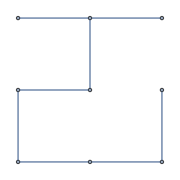

```mathematica
SeedRandom[randomSeed];
Graph[FindRandomGridMazeSolution[{3,3},"maze"],ImageSize->Small]
```

Get the solution:

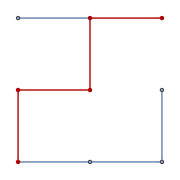

```mathematica
SeedRandom[randomSeed];
Graph[FindRandomGridMazeSolution[{3,3},"solved-maze"],ImageSize->Small]
```

Get data on the maze:

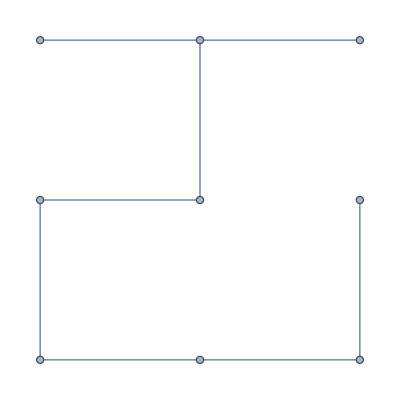
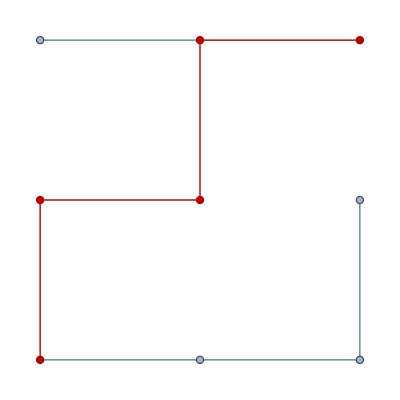
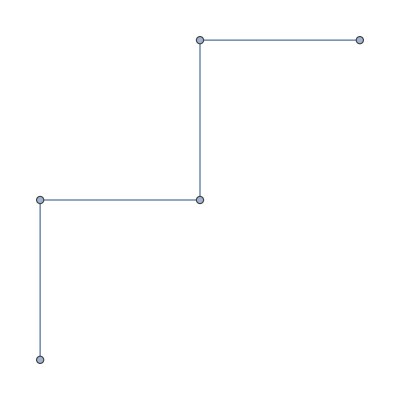
<|maze→-Graphics-,solved-maze→-Graphics-,shortest-path→{1,2,5,6,9},distance→4,start→1,end→9,shortest-path-subgraph→-Graphics-,random-seed→RandomGeneratorState[…],tree→-Graphics-,tree-depth→4,tree-leaves→{-Graphics-,-Graphics-,-Graphics-},tree-leaf-count→3,tree-size→9,dead-ends→{3,8},dead-ends-count→2|>

```mathematica
SeedRandom[randomSeed];
FindRandomGridMazeSolution[{3,3}]
```

Find a solution to a random 5x5 maze:

```mathematica
{maze,randomSeed}=Values@FindRandomGridMazeSolution[{5,5},{"maze","random-seed"}];
```

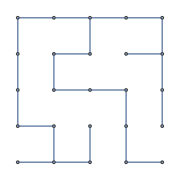

```mathematica
SeedRandom[randomSeed];
Graph[FindRandomGridMazeSolution[{5,5},"maze"],ImageSize->Small]
```

Get the solution:

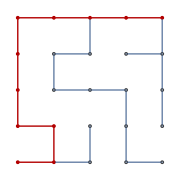

```mathematica
SeedRandom[randomSeed];
Graph[FindRandomGridMazeSolution[{5,5},"solved-maze"],ImageSize->Small]
```

Get data on the maze:

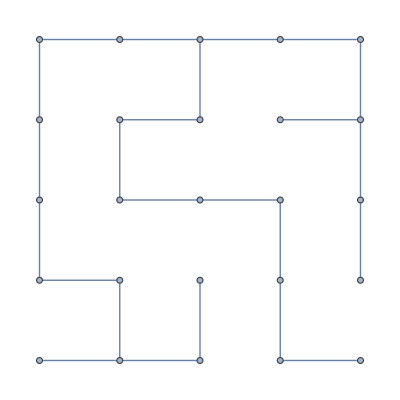
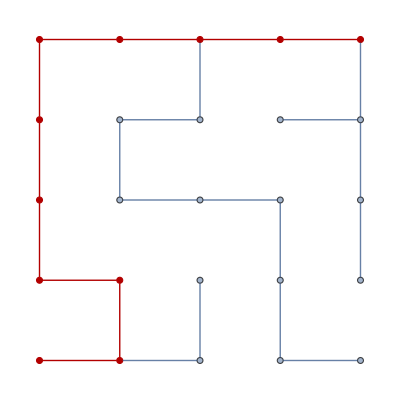
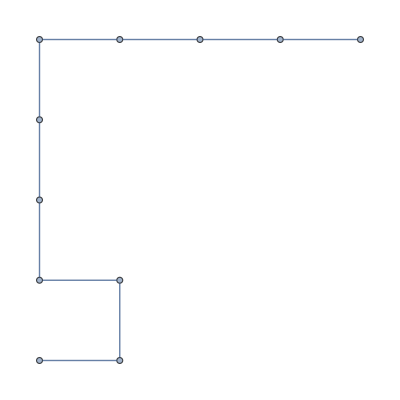
<|maze→-Graphics-,solved-maze→-Graphics-,shortest-path→{1,6,7,2,3,4,5,10,15,20,25},distance→10,start→1,end→25,shortest-path-subgraph→-Graphics-,random-seed→RandomGeneratorState[…],tree→-Graphics-,tree-depth→16,tree-leaves→{-Graphics-,-Graphics-,-Graphics-,-Graphics-},tree-leaf-count→4,tree-size→25,dead-ends→{12,19,21,22},dead-ends-count→4|>

```mathematica
SeedRandom[randomSeed];
FindRandomGridMazeSolution[{5,5}]
```

Find a solution to a random 5x5 maze:

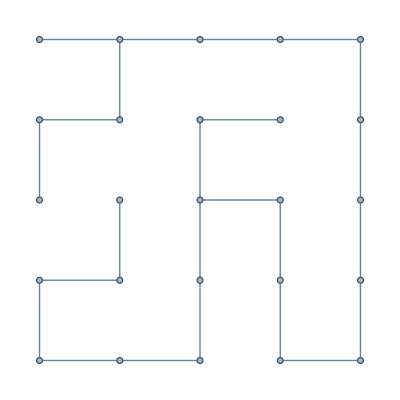
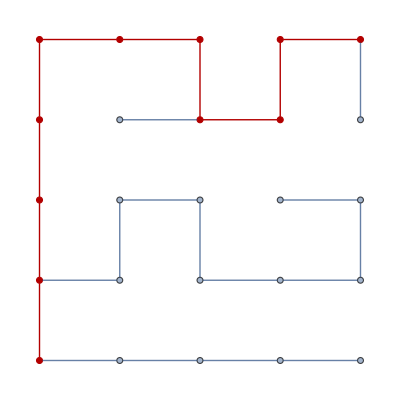
<|maze→-Graphics-,solved-maze→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{5,5},{"maze","solved-maze"}]
```

Find a solution to

Find a solution to a random 20 by 30 maze:

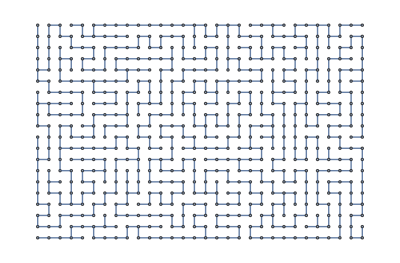
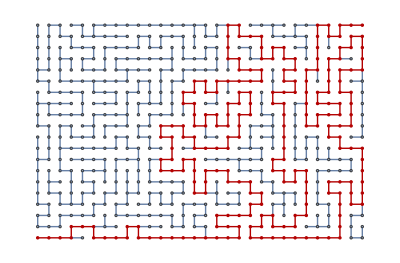
<|maze→-Graphics-,solved-maze→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{20,30}]
```

Find a solution to a random 50 by 60 maze:

```mathematica
FindRandomGridMazeSolution[{50,60}]
```

-Graphics-

Find a solution to a random 60 by 70 maze:

```mathematica
FindRandomGridMazeSolution[{60,70}]
```

-Graphics-

Solve a random 70 by 80 maze:

```mathematica
FindRandomGridMazeSolution[{70,80}]
```

-Graphics-

## Source & Additional Information

### Contributed By

Peter Cullen Burbery

### Keywords

mazes

graph algorithms

fun

### Categories

Cloud & Deployment
 External Interfaces & Connections
 Graphs & Networks
 Knowledge Representation & Natural Language
 Repository Tools
 Strings & Text
 User Interface Construction |  Core Language & Structure
 Financial Data & Computation
 Higher Mathematical Computation
 Machine Learning
 Scientific and Medical Data & Computation
 Symbolic & Numeric Computation
 Visualization & Graphics |  Data Manipulation & Analysis
 Geographic Data & Computation
 Images
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 System Operation & Setup
 Wolfram Physics Project |  Engineering Data & Computation
 Geometry
 Just For Fun
 Programming Utilities
 Sound & Video
 Time-Related Computation

### Related Symbols

FindShortestPath

### Related Resource Objects

RandomMaze

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.